# RBF Limits

The plan is to see what NLA can do with an RBF matrix. You can see (and fix) the dominant low rank structure easily

## In 2D there is a drop off at √m

```mathematica
Clear[A]
m=10^2;
RankOne=KroneckerProduct[ConstantArray[1,m],ConstantArray[1,m]];
xs=RandomReal[{-1,1},{m,2}];
ϕ[ϵ_][r_]:=E^(-(ϵ r)^2)
A[ϵ_]:=A[ϵ]=Table[ϕ[ϵ][Norm[xs⟦i⟧-xs⟦j⟧]^2],{i,m},{j,m}]
ϵs=10.0^Range[-2,-10,-1]
TabView[{
ListPlot[xs],
ListLogLogPlot[
Table[Abs[Eigenvalues[A[ϵ]]],{ϵ,ϵs}],
PlotRange->{10^-18,m},
Joined->True,
PlotLegends->ϵs,
Frame->True,
GridLines->{√m{0.8,1.0,1.2},Automatic}
],
ListLogLogPlot[
Table[Abs[Eigenvalues[A[ϵ]-RankOne]],{ϵ,ϵs}],
PlotRange->{10^-18,10^-1},
Joined->True,
PlotLegends->ϵs,
Frame->True,
GridLines->{√m{0.8,1.0,1.2},Automatic}
]}]
```

{0.01,0.001,0.0001,0.00001,1.×10^-6,1.×10^-7,1.×10^-8,1.×10^-9,1.×10^-10}

123

### The question is what are the eigenvectors saying?

```mathematica
ϵ=10^-5;
V=Eigenvectors[A[ϵ]-RankOne,Ceiling[1.5 √m]];
TabView[{
"Signed"->MatrixPlot[V],
"Leverage Scores?"->MatrixPlot[(V)^2]
}
]
```

12

```mathematica
TabView[Table[ListPlot[v,PlotRange->All],{v, V}]]
```

123456789101112131415

## In 3D there is a drop off at m^(1/3)

```mathematica
Clear[A]
m=10^3;
RankOne=KroneckerProduct[ConstantArray[1,m],ConstantArray[1,m]];
xs=RandomReal[{-1,1},{m,3}];
ϕ[ϵ_][r_]:=E^(-(ϵ r)^2)
A[ϵ_]:=A[ϵ]=Table[ϕ[ϵ][Norm[xs⟦i⟧-xs⟦j⟧]^2],{i,m},{j,m}]
ϵs=10.0^Range[-2,-10,-1]
TabView[{
ListPointPlot3D[xs],
ListLogLogPlot[
Table[Abs[Eigenvalues[A[ϵ]]],{ϵ,ϵs}],
PlotRange->{10^-18,m},
Joined->True,
PlotLegends->ϵs,
Frame->True,
GridLines->{m^(1/3){0.8,1.0,1.2},Automatic}
],
ListLogLogPlot[
Table[Abs[Eigenvalues[A[ϵ]-RankOne]],{ϵ,ϵs}],
PlotRange->{10^-18,10^-1},
Joined->True,
PlotLegends->ϵs,
Frame->True,
GridLines->{m^(1/3){0.8,1.0,1.2},Automatic}
]}]
```

{0.01,0.001,0.0001,0.00001,1.×10^-6,1.×10^-7,1.×10^-8,1.×10^-9,1.×10^-10}

123

# Pade

The plan is to see what NLA can do with an RBF matrix. You can see (and fix) the dominant low rank structure easily

(1-ϵr^2/2)/(1+ϵr^2/2)

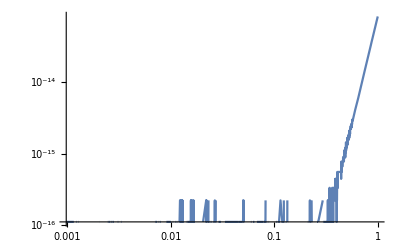

```mathematica
Clear[f,p,ϵ,r]
f[ϵ_,r_]:=E^(-(ϵ r)^2)
p[ϵr_]=PadeApproximant[f[ϵr,1],{ϵr,0,{3,2}}]
ϵ=0.01;
LogLogPlot[{Abs[f[ϵ,r]-p[ϵ r]]},{r,0, 100 ϵ},
PlotRange->All]
```

## In 2D there is a drop off at √m

```mathematica
Clear[A]
m=10^2;
RankOne=KroneckerProduct[ConstantArray[1,m],ConstantArray[1,m]];
xs=RandomReal[{-1,1},{m,2}];
ϕ[ϵ_][r_]:=E^(-(ϵ r)^2)
A[ϵ_]:=A[ϵ]=Table[ϕ[ϵ][Norm[xs⟦i⟧-xs⟦j⟧]^2],{i,m},{j,m}]
ϵs=10.0^Range[-2,-10,-1]
TabView[{
ListPlot[xs],
ListLogLogPlot[
Table[Abs[Eigenvalues[A[ϵ]]],{ϵ,ϵs}],
PlotRange->{10^-18,m},
Joined->True,
PlotLegends->ϵs,
Frame->True,
GridLines->{√m{0.8,1.0,1.2},Automatic}
],
ListLogLogPlot[
Table[Abs[Eigenvalues[A[ϵ]-RankOne]],{ϵ,ϵs}],
PlotRange->{10^-18,10^-1},
Joined->True,
PlotLegends->ϵs,
Frame->True,
GridLines->{√m{0.8,1.0,1.2},Automatic}
]}]
```

{0.01,0.001,0.0001,0.00001,1.×10^-6,1.×10^-7,1.×10^-8,1.×10^-9,1.×10^-10}

123

## In 3D there is a drop off at m^(1/3)

```mathematica
Clear[A]
m=10^3;
RankOne=KroneckerProduct[ConstantArray[1,m],ConstantArray[1,m]];
xs=RandomReal[{-1,1},{m,3}];
ϕ[ϵ_][r_]:=E^(-(ϵ r)^2)
A[ϵ_]:=A[ϵ]=Table[ϕ[ϵ][Norm[xs⟦i⟧-xs⟦j⟧]^2],{i,m},{j,m}]
ϵs=10.0^Range[-2,-10,-1]
TabView[{
ListPointPlot3D[xs],
ListLogLogPlot[
Table[Abs[Eigenvalues[A[ϵ]]],{ϵ,ϵs}],
PlotRange->{10^-18,m},
Joined->True,
PlotLegends->ϵs,
Frame->True,
GridLines->{m^(1/3){0.8,1.0,1.2},Automatic}
],
ListLogLogPlot[
Table[Abs[Eigenvalues[A[ϵ]-RankOne]],{ϵ,ϵs}],
PlotRange->{10^-18,10^-1},
Joined->True,
PlotLegends->ϵs,
Frame->True,
GridLines->{m^(1/3){0.8,1.0,1.2},Automatic}
]}]
```

{0.01,0.001,0.0001,0.00001,1.×10^-6,1.×10^-7,1.×10^-8,1.×10^-9,1.×10^-10}

123